```mathematica
description="Learning FeynCalc through examples.";
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

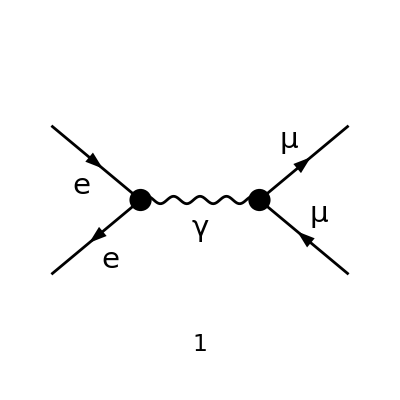

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes},Restrictions->QEDOnly];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple, SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[p3, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(3\)]\)"; 
MakeBoxes[p4, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(4\)]\)";
```

```mathematica
amp[0]=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{p3,p4},
ChangeDimension->4,
List->False,
UndoChiralSplittings->True,
Contract->True,
SMP->True
]
```

-(e^2 (φ(-OverBar[p_2],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_μ)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_μ)))/(OverBar[p_3]+OverBar[p_4])^2

```mathematica
ampPolarized[0]=amp[0]/.{
Spinor[-Momentum[p4],r__]:>
GA[6].Spinor[-Momentum[p4],r],
Spinor[Momentum[p3],r__]:>
Spinor[Momentum[p3],r].GA[7],
Spinor[Momentum[p1],r__]:>
GA[6].Spinor[Momentum[p1],r],
Spinor[-Momentum[p2],r__]:>
Spinor[Momentum[p2],r].GA[7]
}
```

-(e^2 (φ(OverBar[p_2],m_e)).(γ̄)^7.(γ̄)^Lor2.(γ̄)^6.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_μ)).(γ̄)^7.(γ̄)^Lor2.(γ̄)^6.(φ(-OverBar[p_4],m_μ)))/(OverBar[p_3]+OverBar[p_4])^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_e"],SMP["m_mu"],SMP["m_mu"]];
```

```mathematica
ampSquared[0]=(amp[0](ComplexConjugate[amp[0]]))
```

e^4 (1/(OverBar[p_3]+OverBar[p_4])^2)^2 (φ(-OverBar[p_2],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_μ)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_μ)) (φ(OverBar[p_1],m_e)).(γ̄)^($AL($109)).(φ(-OverBar[p_2],m_e)) (φ(-OverBar[p_4],m_μ)).(γ̄)^($AL($109)).(φ(OverBar[p_3],m_μ))

```mathematica
ampSquared[1]=ampSquared[0]//FeynAmpDenominatorExplicit
```

(e^4 (φ(-OverBar[p_2],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_μ)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_μ)) (φ(OverBar[p_1],m_e)).(γ̄)^($AL($109)).(φ(-OverBar[p_2],m_e)) (φ(-OverBar[p_4],m_μ)).(γ̄)^($AL($109)).(φ(OverBar[p_3],m_μ)))/s^2

```mathematica
ampSquared[2]=ampSquared[1]//FermionSpinSum[#,ExtraFactor->1/2^2]&
```

(e^4 tr((γ̄·OverBar[p_1]+m_e).(γ̄)^($AL($109)).(γ̄·OverBar[p_2]-m_e).(γ̄)^Lor2) tr((γ̄·OverBar[p_3]+m_μ).(γ̄)^Lor2.(γ̄·OverBar[p_4]-m_μ).(γ̄)^($AL($109))))/(4 s^2)

```mathematica
ampSquared[3]=ampSquared[2]//DiracSimplify
```

(8 e^4 m_e^2 m_μ^2)/s^2-(4 e^4 t m_e^2)/s^2-(4 e^4 u m_e^2)/s^2+(4 e^4 m_e^4)/s^2+(4 e^4 m_e^2)/s+(4 e^4 m_μ^4)/s^2-(4 e^4 t m_μ^2)/s^2-(4 e^4 u m_μ^2)/s^2+(4 e^4 m_μ^2)/s+(2 e^4 t^2)/s^2+(2 e^4 u^2)/s^2

```mathematica
ampSquared[4]=ampSquared[3]//Simplify
```

(2 e^4 (2 m_e^2 (2 m_μ^2+s-t-u)+2 m_e^4+2 m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
ampSquaredPolarized[0]=(ampPolarized[0](ComplexConjugate[ampPolarized[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum//DiracSimplify//Simplify
```

(4 e^4 (m_e^2+m_μ^2-u)^2)/s^2

```mathematica
ampSquaredMassless1[0]=ampSquared[4]//ReplaceAll[#,{SMP["m_e"]->0}]&
```

(2 e^4 (2 m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
ampSquaredMassless2[0]=ampSquared[4]//ReplaceAll[#,{SMP["m_e"]->0,SMP["m_mu"]->0}]&
```

(2 e^4 (t^2+u^2))/s^2

```mathematica
ampSquaredPolarizedMassless[0]=ampSquaredPolarized[0]//ReplaceAll[#,{SMP["m_e"]->0,SMP["m_mu"]->0}]&
```

(4 e^4 u^2)/s^2

```mathematica
prefac1=1/(64Pi^2s)
```

1/(64 π^2 s)

```mathematica
integral1=(Factor[ampSquaredMassless2[0]/.{t->-s/2(1-Cos[Th]),u->-s/2(1+Cos[Th]),SMP["e"]^4->(4Pi SMP["alpha_fs"])^2}])
```

16 π^2 α^2 (cos^2(Th)+1)

```mathematica
diffXSection1=prefac1 integral1
```

(α^2 (cos^2(Th)+1))/(4 s)

```mathematica
prefac2=1/(128 Pi^2 s)
```

1/(128 π^2 s)

```mathematica
integral2=Simplify[ampSquaredMassless2[0]/(s/4)/.{u->-s-t,SMP["e"]^4->(4 Pi SMP["alpha_fs"])^2}]
```

(128 π^2 α^2 (s^2+2 s t+2 t^2))/s^3

```mathematica
diffXSection2=prefac2 integral2
```

(α^2 (s^2+2 s t+2 t^2))/s^4

```mathematica
2Pi Integrate[diffXSection1 Sin[Th],{Th,0,Pi}]
```

(4 π α^2)/(3 s)

```mathematica
crossSectionTotal=2 Pi Integrate[diffXSection2,{t,-s,0}]
```

(4 π α^2)/(3 s)

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
DiracGamma[6]
```

(γ̄)^6

```mathematica
DiracSubstitute67[%]
```

(γ̄)^5/2+1/2

```mathematica
g6=DiracGamma[6]
g7=DiracGamma[7]
```

(γ̄)^6

(γ̄)^7

```mathematica
DiracSubstitute67[g6]
```

(γ̄)^5/2+1/2

```mathematica
DiracSubstitute67[g7]
```

1/2-(γ̄)^5/2

```mathematica
g5=DiracGamma[5]
```

(γ̄)^5

```mathematica
DiracSubstitute5[g5]
```

(γ̄)^6-(γ̄)^7

```mathematica
f=a x+b y + c x^2
```

a x+b y+c x^2

```mathematica
InputForm[Part[f,0]]
```

Plus

```mathematica
PR=GA[6]
```

(γ̄)^6

```mathematica
Mγ[0]
```

-1/(p_3+p_4)^2 ⅈ e IndexDelta(A,B) (2/3 ⅈ e δ_Col1Col2 (φ(p_1,MQU(QuarkGen))).(γ̄)^6.(γ·(p_3-p_4)).(φ(-p_2,MQU(QuarkGen)))+2/3 ⅈ e δ_Col1Col2 (φ(p_1,MQU(QuarkGen))).(γ̄)^7.(γ·(p_3-p_4)).(φ(-p_2,MQU(QuarkGen))))

```mathematica
ComplexConjugate[PR]
```

(γ̄)^7

```mathematica
G5=GA[5]
```

(γ̄)^5

```mathematica
PL=GA[7]
```

(γ̄)^7

```mathematica
DiracSubstitute67[PL]
```

1/2-(γ̄)^5/2

```mathematica
DiracSubstitute67[PR]
```

(γ̄)^5/2+1/2

```mathematica
ComplexConjugate[G5]
```

-(γ̄)^5

```mathematica
GM=GA[μ]
```

(γ̄)^μ

```mathematica
ComplexConjugate[GM]
```

(γ̄)^μ

```mathematica
u=Spinor[q1,m1]
```

φ(q1,m1)

```mathematica
v=Spinor[-q2,m2]
```

φ(-q2,m2)

```mathematica
exp=u.GM. GM.v.MT[μ,ν]
```

(φ(q1,m1)).(γ̄)^μ.(γ̄)^μ.(φ(-q2,m2)).(ḡ)^μν

```mathematica
ComplexConjugate[exp]
```

FermionSpinSum::failmsg: Error! FermionSpinSum encountered a fatal problem and must abort the computation. The problem reads: The input contains Spinor objects with incorrect syntax.

$Aborted

```mathematica
exp=Spinor[p1,m].GS[p1].Spinor[-p2,m]
```

(φ(p_1,m)).(γ̄·OverBar[p_1]).(φ(-p_2,m))

```mathematica
ComplexConjugate[exp]
```

FermionSpinSum::failmsg: Error! FermionSpinSum encountered a fatal problem and must abort the computation. The problem reads: The input contains Spinor objects with incorrect syntax.

$Aborted

```mathematica
exp=GA[μ,ν,ρ]
```

(γ̄)^μ.(γ̄)^ν.(γ̄)^ρ

```mathematica
ComplexConjugate[exp]
```

(γ̄)^ρ.(γ̄)^ν.(γ̄)^μ

```mathematica
u=Spinor[Momentum[p1],m1];
v=Spinor[-Momentum[p2],m2];
gammas=(a GA[6]+b GA[7]+c GA[5]);
exp=u.gammas.v
ComplexConjugate[exp]
```

(φ(OverBar[p_1],m1)).(a (γ̄)^6+b (γ̄)^7+c (γ̄)^5).(φ(-OverBar[p_2],m2))

(φ(-OverBar[p_2],m2)).(a (γ̄)^7+b (γ̄)^6-c (γ̄)^5).(φ(OverBar[p_1],m1))

```mathematica
t0=a+b+a^2+b^2+2a b
```

a^2+2 a b+a+b^2+b

```mathematica
Isolate[t0]
```

KK(187)

```mathematica
t0
```

a^2+2 a b+a+b^2+b

```mathematica
Isolate[t0,a+b]
```

KK(187)

```mathematica
t0
```

a^2+2 a b+a+b^2+b

```mathematica
t0=Isolate[a+b]
```

KK(188)

```mathematica
t1=a^2+b^2+2 a b+a + b
```

a^2+2 a b+a+b^2+b

```mathematica
t2=Isolate[t1,c]
```

KK(187)

```mathematica
t2
```

KK(187)

```mathematica
t1
```

a^2+2 a b+a+b^2+b

```mathematica
Information[KK]
```

```mathematica
t1
```

a^2+2 a b+a+b^2+b

```mathematica
Collect2[t2,a+b]
```

KK(187)

```mathematica
Collect2[t1,a+b]
```

(a+b) (a+b+1)

```mathematica
TemporalMomentum[k]
```

k

```mathematica
Momentum[k]
```

k̄

```mathematica
TemporalMomentum[k]
```

k

```mathematica
k
```

k

```mathematica
Integrate[t,{Th,0,Pi}]
```

π t

```mathematica
<<FeynCalc`
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

```mathematica
GS[Momentum[q]].GA[μ].GA[5].GS[Momentum[p]]
```

(γ̄·q̄).(γ̄)^μ.(γ̄)^5.(γ̄·p̄)

```mathematica
ComplexConjugate[%]
```

-(γ̄·p̄).(γ̄)^5.(γ̄)^μ.(γ̄·q̄)

```mathematica
(1+GA[5])(1-GA[5])//Expand
```

1-((γ̄)^5)^2

```mathematica
GA[5].GA[5]
```

(γ̄)^5.(γ̄)^5

```mathematica
psi=Spinor[Momentum[p]]
```

φ(p̄)

```mathematica
Pair[Momentum[p],psi]
```

Pair(p̄,φ(p̄))

```mathematica
Spinor[-Momentum[p],0,1].DiracGamma[Momentum[q]].Spinor[Momentum[p],0,1]
```

(φ(-p̄)).(γ̄·q̄).(φ(p̄))

```mathematica
M[0][[9]]
```

(ⅈ e^2 (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-OverBar[p_2],MQU(quarkGen))).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))))/(2 (cos(θ_W)) (sin(θ_W)) ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2) ((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

```mathematica
M[0][[5]]
```

-((2 e^3 δ_Col1Col2 IndexDelta(A,B) (-(k̄·(ε̄)^*(k))-2 (OverBar[p4]·(ε̄)^*(k))) (φ(-OverBar[p2],MQU(quarkGen))).(γ̄·(k̄-OverBar[p3]+OverBar[p4])).(φ(OverBar[p1],MQU(quarkGen))))/(3 (k̄+OverBar[p3]+OverBar[p4])^2 ((k̄+OverBar[p4])^2-(MSf(A,2,i))^2)))